## ψ_(++)(x_1,x_2), ψ_(+-)(x_1,x_2), ψ_(-+)(x_1,x_2) and ψ_(--)(x_1,x_2)

```mathematica
ψ1[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 + σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];, ψ_(++)
ψ2[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 -n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ3[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ (σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(-ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ4[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(-n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
ψ[n_,x1_,x2_,σ1_,σ2_,θ_]:=-(ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ(σ1 + σ2 + n θ))+(ⅇ^(ⅈ 2θ))^k ⅇ^(ⅈ(σ1 -n θ))+(ⅇ^(-ⅈ 2θ))^k ⅇ^(ⅈ (σ2 + n θ))+ⅇ^(ⅈ(-n θ)))Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
```

## Effects of losses (Assumption: ψ_(+-)(x,x) and ψ_(-+)(x,x) amplitudes are negligible after post selection on x=√N)

```mathematica
P[j_,n_,x_,σ1_,σ2_,θ_,t_,R_]:=Module[{f,α,β,ψpp,ψmm,outPhase},
outPhase={{1,ⅈ^2,ⅈ^2,ⅈ^4},{ⅈ,ⅈ^3,ⅈ,ⅈ^3},{ⅈ,ⅈ,ⅈ^3,ⅈ^3},{ⅈ^2,ⅈ^2,ⅈ^2,ⅈ^2}};
α=ⅈ √(1-t^2)R/(√2)ⅇ^(+ⅈ θ);
β=ⅈ √(1-t^2)R/(√2)ⅇ^(-ⅈ θ);
f=ⅇ^(-(Abs[β]^2+Abs[α]^2+2β* α));
ψpp=ψ1[n,x,x,σ1,σ2,θ];
ψmm=ψ4[n,x,x,σ1,σ2,θ];
Abs[ t^n ⅇ^((1-t^2)R^2/2)]^2(Abs[outPhase[[j,1]]ψpp]^2+Abs[outPhase[[j,4]]ψmm]^2+2Re[ f (outPhase[[j,1]]ψpp)* (outPhase[[j,4]]ψmm)])
];
```

NOTE : This expression is sensitive to R, whereas earlier we had seen that R can be arbitrary.
This arises while making the assumption that a single coherent state can be pulled out of the integral over ϕ.

#### Plots

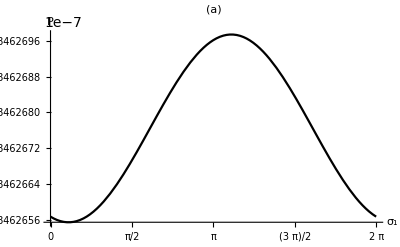

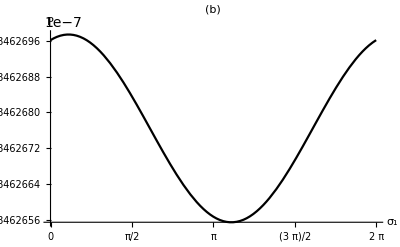

```mathematica
t=0.6;
n=24;R=√n;p1=Plot[P[4,n,√n,σ1,0,π/4,t,R],{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->30]]
p2=Plot[P[4,n,√n,σ1,π,π/4,t,R],{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->30]]
```

## CHSH Bell’s inequality considering loss (and no binning for homodyne measurement)

### Calculating the expectation value:- ⟨ab⟩

```mathematica
LossyExpec1[n_,σ1_,σ2_,θ_,t_,R_]:=
Module[{i,j,k,l},
i=P[1,n,√n,σ1,σ2,θ,t,R];
j=P[2,n,√n,σ1,σ2,θ,t,R];
k=P[3,n,√n,σ1,σ2,θ,t,R];
l=P[4,n,√n,σ1,σ2,θ,t,R];
N[(i-j-k+l)/(i+j+k+l)]];
LossyS1[n_,θ_,a_,b_,aprime_,bprime_,t_,R_]:=Abs[LossyExpec1[n,a,b,θ,t,R]+LossyExpec1[n,a,bprime,θ,t,R]+LossyExpec1[n,aprime,b,θ,t,R]-LossyExpec1[n,aprime,bprime,θ,t,R]];
```

## Plots

#### S should not be sensitive to R. This is expected as the number state written in terms of coherent states on a circle allows for arbitrary R.

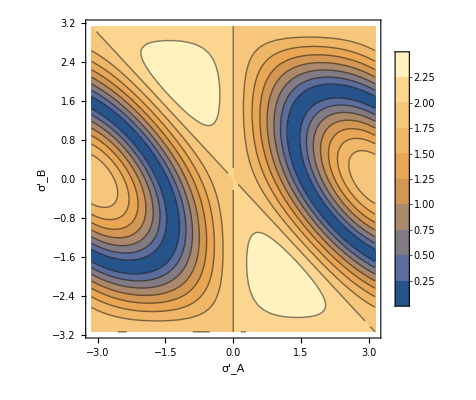

```mathematica
n=24;
t=1;
R=1;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
n=24;
t=1;
R=√24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

-Graphics-

```mathematica
n=24;
t=1;
R=24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

-Graphics-

#### For t = 1 we see that S is independent of R

## Now we look at the case where t ≠ 1 (losses) with the approximation

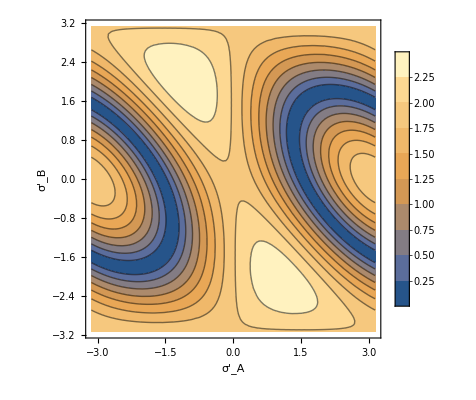

```mathematica
n=24;
t=0.99;
R=1;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

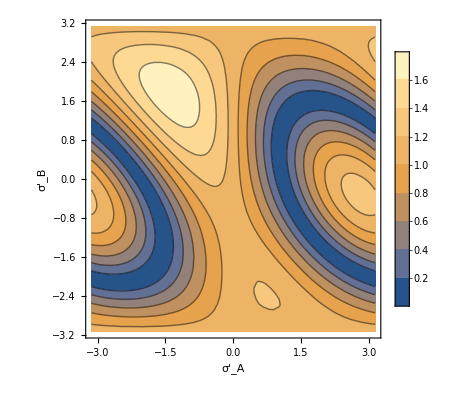

```mathematica
n=24;
t=0.99;
R=√24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

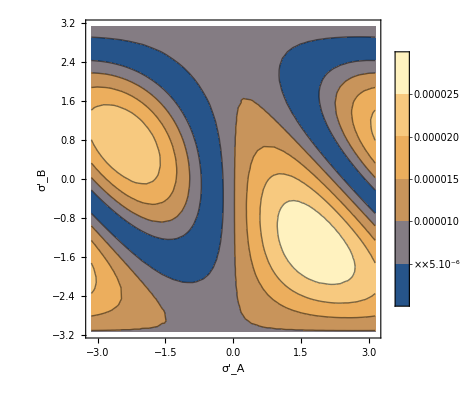

```mathematica
n=24;
t=0.99;
R=24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

As R is arbitrary, we can choose R>>1 so the approximations are valid. However, we see that for large R, S drops rapidly.

## Intermediate plots

```mathematica
ψbefore[n_,x1_,x2_]:=(ⅇ^(-(x1^2+x2^2)/2))/(√(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];
∫_(-∞)^∞ ∫_(-∞)^∞ Abs[ψbefore[5,x1,x2]]^2 ⅆx1ⅆx2
```

1

```mathematica
(*Export["g9.gif", g[9], "AnimationRepetitions" -> ∞]*)
```

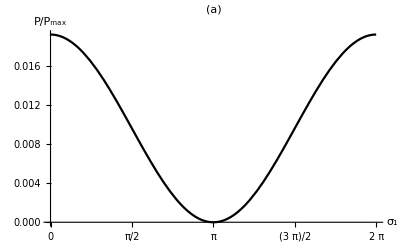

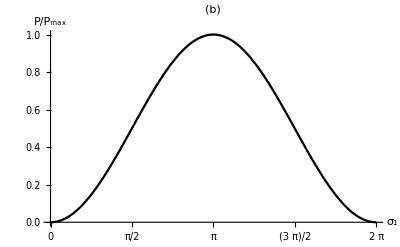

```mathematica
p1=Plot[Abs[ψ[24,(√24)/1,(√24)/1,σ1,0,π/4]]^2,{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P/P_max"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->30]]
p2=Plot[Abs[ψ[24,(√24)/1,(√24)/1,σ1,π,π/4]]^2/FindMaximum[Abs[ψ[24,(√24)/1,(√24)/1,x,π,π/4]]^2,{x,π}][[1]],{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P/P_max"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->30]]
```

```mathematica
Export["24pi4bell.emf",GraphicsRow[{p1,p2}]]
```

24pi4bell.emf

```mathematica
(*p3=Plot[Abs[ψ[8,√8,√8,σ1,0,π/8]]^2,{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->30]];
p4=Plot[Abs[ψ[7,√7,-√7,σ1,0,π/8]]^2,{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->30]];*)
```

```mathematica
(*BellIneq= Import[Export["BellIneq.pdf",GraphicsRow[{p1,p2}],ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["BellIneq.emf",BellIneq[[1]],ImageResolution->1000]*)
```

```mathematica
(*Export["p.emf",p1]*)
```

```mathematica
(*m[n_]:=Manipulate[GraphicsRow[{pr[σ2,2π],cm[σ2,2π]}],{σ2,0,2π,Appearance->"Open"}];
m[4]*)
```

```mathematica
(*DensityPlot[Cos[(x1-x2)/2]^2,{x1,-π,π},{x2,-π,π}]*)
(*manipulate = Manipulate[ContourPlot[Abs[ψ[4,2,2,σ1,σ2,θ]]^2,{σ1,-π,π},{σ2,-π,π},AxesLabel->{"σ1","σ2"}, Mesh->Full,PlotLegends->Placed[Automatic, Right]],{θ,0.1,2π}]*)
```

```mathematica
ψbefore[n_,x1_,x2_]:=(ⅇ^(-(x1^2+x2^2)/2))/(√(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
```

```mathematica
(*∫_(-∞)^∞ ∫_(-∞)^∞ Abs[ψbefore[6,x1,x2]]^2 ⅆx1ⅆx2*)
```

```mathematica
p5=Plot3D[Abs[ψ1[24,x1,x2,0,0,π/4]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x_1","x_2"},PlotLegends->Automatic,PlotPoints->200,Axes->{True,True,False},LabelStyle->{FontSize->30,FontFamily->"Cambria Math", Black},PlotStyle->Opacity[0.9],ColorFunction->"Rainbow",Mesh->None,PlotLabel-> Style["|ψ_(±±)|^2" ,FontFamily->"Cambria Math",FontSize->30],ImageSize->Scaled[0.8]]
p6=Plot3D[Abs[ψ2[24,x1,x2,0,0,π/4]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x_1","x_2"},PlotLegends->Automatic,PlotPoints->200,Axes->{True,True,False},LabelStyle->{FontSize->30,FontFamily->"Cambria Math", Black},PlotStyle->Opacity[0.9],ColorFunction->"Rainbow",Mesh->None,PlotLabel-> Style["|ψ_(±∓)|^2",FontFamily->"Cambria Math",FontSize->30],ImageSize->Scaled[0.8]]
```

-Graphics3D-

-Graphics3D-

```mathematica
p5plt= Import[Export["p5.pdf",p5,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p5.emf",p5plt[[1]],ImageResolution->1000]
p6plt= Import[Export["p6.pdf",p6,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p6.emf",p6plt[[1]],ImageResolution->1000]
p7=GraphicsColumn[{p5plt[[1]],p6plt[[1]]}];
p7plt= Import[Export["p7.pdf",p7,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p7.emf",p7plt[[1]],ImageResolution->1000]
```

p5.emf

p6.emf

p7.emf

```mathematica
p7=ContourPlot[Abs[ψ3[24,x1,x2,0,0,π/8]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x1","x2"},Mesh->None,PlotPoints->50,Mesh->Full,Axes->True,LabelStyle->{FontSize->15,FontFamily->"Times", Black},Contours->5,GridLines->{{√24}, {√24}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}}];
p8=ContourPlot[Abs[ψ1[24,x1,x2,0,0,π/8]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x1","x2"},Mesh->None,PlotPoints->50,Mesh->Full,Axes->True,LabelStyle->{FontSize->15,FontFamily->"Times", Black},Contours->5,GridLines->{{√24}, {√24}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}}];
Export["24pi81.emf",GraphicsRow[{p7,p8}]]
```

24pi81.emf

```mathematica
(*P=∫_(0.995 √24)^(1.005 √24) ∫_(0.995 √24)^(1.005 √24) Abs[ψ[24,x1,x2,0,0,π/4]]^2 ⅆx1ⅆx2;*)
```

```mathematica
blurryP[n_,σ1_,σ2_,θ_]:=Abs[NIntegrate[ψ[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,.95 √n,1.05 √n}]]^2;
```

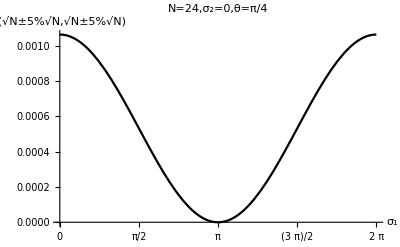

```mathematica
pblurry024=Plot[blurryP[24,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

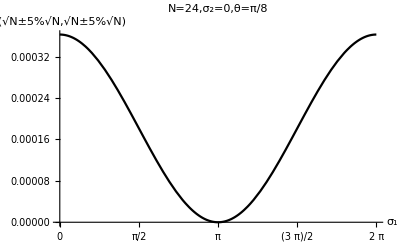

```mathematica
pblurry8024=Plot[blurryP[24,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

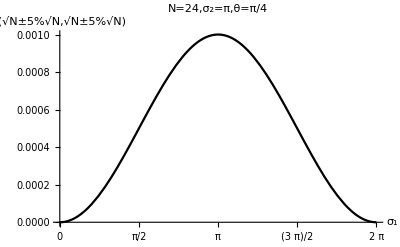

```mathematica
pblurrypi24=Plot[blurryP[24,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

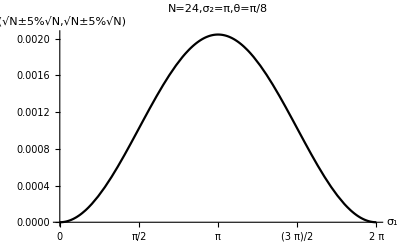

```mathematica
pblurry8pi24=Plot[blurryP[24,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

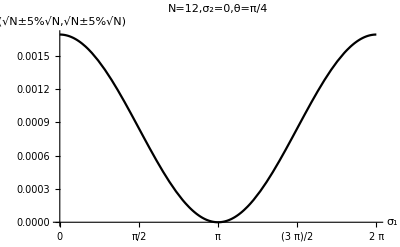

```mathematica
pblurry012=Plot[blurryP[12,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

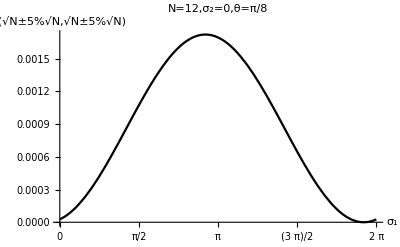

```mathematica
pblurry12012=Plot[blurryP[12,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

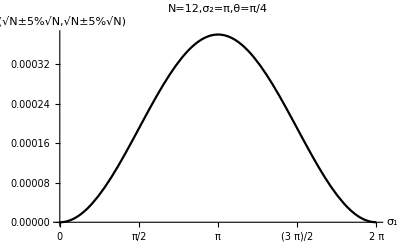

```mathematica
pblurrypi12=Plot[blurryP[12,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

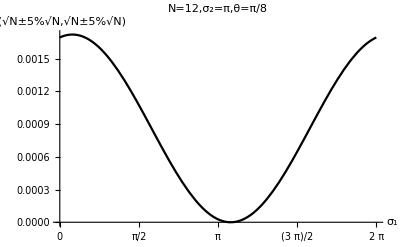

```mathematica
pblurry8pi12=Plot[blurryP[12,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

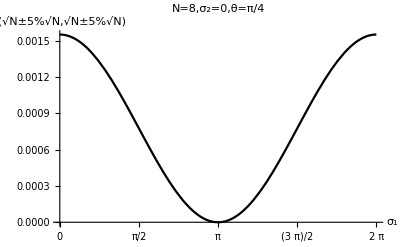

```mathematica
pblurry08=Plot[blurryP[8,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

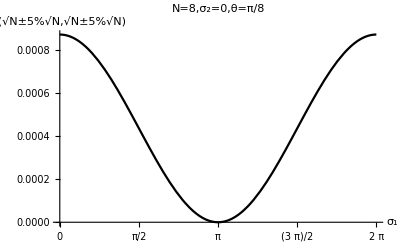

```mathematica
pblurry808=Plot[blurryP[8,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

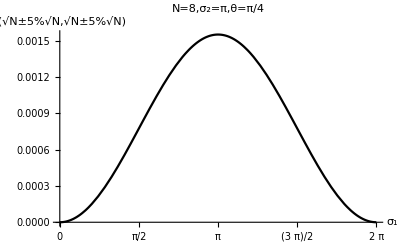

```mathematica
pblurrypi8=Plot[blurryP[8,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

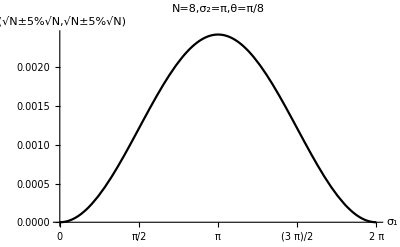

```mathematica
pblurry8pi8=Plot[blurryP[8,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

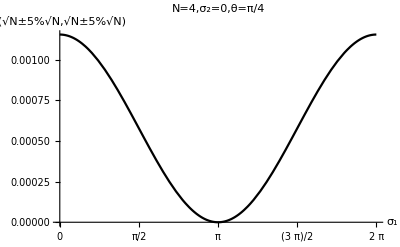

```mathematica
pblurrypi04=Plot[blurryP[4,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

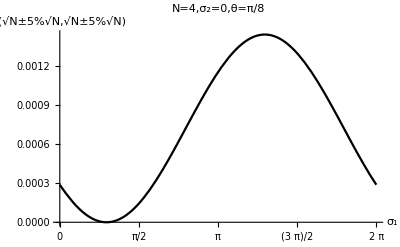

```mathematica
pblurry8pi04=Plot[blurryP[4,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

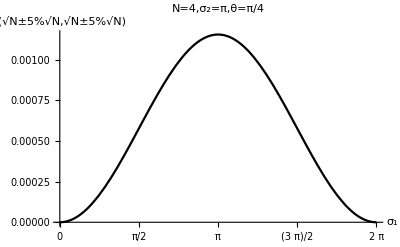

```mathematica
pblurrypi4=Plot[blurryP[4,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

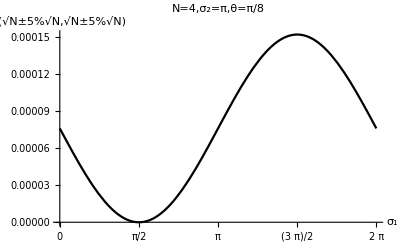

```mathematica
pblurry8pi4=Plot[blurryP[4,σ1,3π/2,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

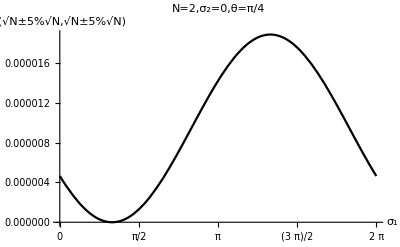

```mathematica
pblurry2pi4=Plot[blurryP[2,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=2,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

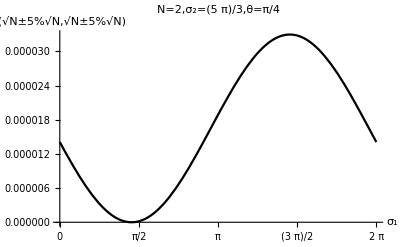

```mathematica
pblurry25pi3pi4=Plot[blurryP[2,σ1,(5π)/3,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=2,σ_2=(5  π)/3,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

## CHSH Inequality

```mathematica
cpp[n_,x1_,x2_,σ1_,σ2_,θ_]:=ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^4 ψ4[n,x1,x2,σ1,σ2,θ];
cpm[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ4[n,x1,x2,σ1,σ2,θ];
cmp[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ4[n,x1,x2,σ1,σ2,θ];
cmm[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ^2 ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ4[n,x1,x2,σ1,σ2,θ];
call[n_,x1_,x2_,σ1_,σ2_,θ_]:=√(Abs[cpp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cpm[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmm[n,x1,x2,σ1,σ2,θ]]^2);
ppp[n_,x1_,x2_,σ1_,σ2_,θ_]:=cpp[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
ppm[n_,x1_,x2_,σ1_,σ2_,θ_]:=cpm[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
pmp[n_,x1_,x2_,σ1_,σ2_,θ_]:=cmp[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
pmm[n_,x1_,x2_,σ1_,σ2_,θ_]:=cmm[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
Expec1[n_,x1_,x2_,σ1_,σ2_,θ_]:=
Module[{i,j,k,l,e,f,g,h},
i=ψ1[n,x1,x2,σ1,σ2,θ];
j=ψ2[n,x1,x2,σ1,σ2,θ];
k=ψ3[n,x1,x2,σ1,σ2,θ];
l=ψ4[n,x1,x2,σ1,σ2,θ];
e=Abs[i+ⅈ^2 j+ⅈ^2 k+ⅈ^4 l]^2;
f=Abs[ⅈ i+ⅈ^3 j+ⅈ k+ⅈ^3 l]^2;
g=Abs[ⅈ i+ⅈ j+ⅈ^3 k+ⅈ^3 l]^2;
h=Abs[ⅈ^2 i+ⅈ^2 j+ⅈ^2 k+ⅈ^2 l]^2;
N[(e-f-g+h)/(e+f+g+h)]];
S1[n_,x1_,x2_,θ_,a_,b_,aprime_,bprime_]:=Abs[Expec1[n,x1,x2,a,b,θ]+Expec1[n,x1,x2,a,bprime,θ]+Expec1[n,x1,x2,aprime,b,θ]-Expec1[n,x1,x2,aprime,bprime,θ]];
```

```mathematica
Expec2[n_,σ1_,σ2_,θ_,Δ_]:=
Module[{e,f,g,h},
e=NIntegrate[Abs[cpp[n,x1,x2,σ1,σ2,θ]]^2,{x1,(1-Δ/2)√n,(1+Δ/2)√n},{x2,(1-Δ/2)√n,(1+Δ/2)√n}];
f=NIntegrate[Abs[cpm[n,x1,x2,σ1,σ2,θ]]^2,{x1,(1-Δ/2)√n,(1+Δ/2)√n},{x2,(1-Δ/2)√n,(1+Δ/2)√n}];
g=NIntegrate[Abs[cmp[n,x1,x2,σ1,σ2,θ]]^2,{x1,(1-Δ/2)√n,(1+Δ/2)√n},{x2,(1-Δ/2)√n,(1+Δ/2)√n}];
h=NIntegrate[Abs[cmm[n,x1,x2,σ1,σ2,θ]]^2,{x1,(1-Δ/2)√n,(1+Δ/2)√n},{x2,(1-Δ/2)√n,(1+Δ/2)√n}];
N[(e-f-g+h)/(e+f+g+h)]
];
S2[n_,θ_,a_,b_,aprime_,bprime_,Δ_]:=Abs[Expec2[n,a,b,θ,Δ]+Expec2[n,a,bprime,θ,Δ]+Expec2[n,aprime,b,θ,Δ]-Expec2[n,aprime,bprime,θ,Δ]];
```

```mathematica
(*ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,1-.01,1+0.01},{bprime,-2.5+0.01,-2.5+.01},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]*)
```

```mathematica
S2[2,π/4,0,5π/3,1.6,2,0.10]
```

1.8021

```mathematica
S2[6,π/4,0,π,1,-2,0.10]
```

2.24738

```mathematica
Expec1[2,√2,√2,0,5π/3,π/4]
```

-0.253846

## Zero bin width

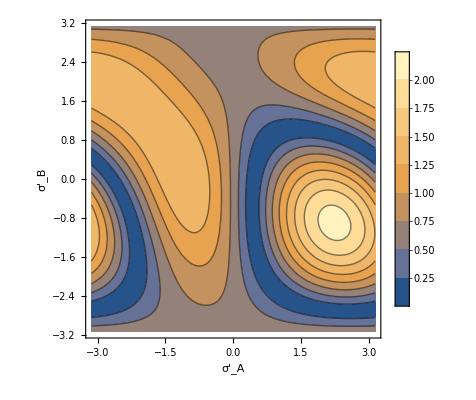

```mathematica
n=1;ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,2},{y,-1}]
```

{2.10808,{x→2.24069,y→-0.900902}}

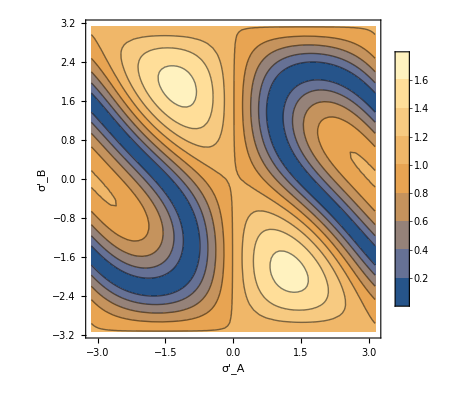

```mathematica
n=2;ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

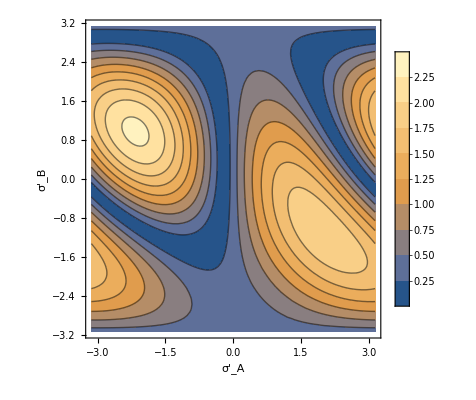

```mathematica
n=3;ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

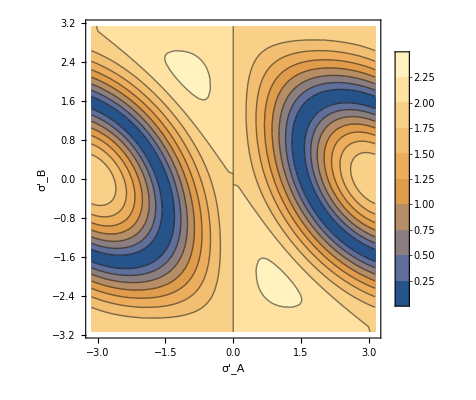

```mathematica
n=4;ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

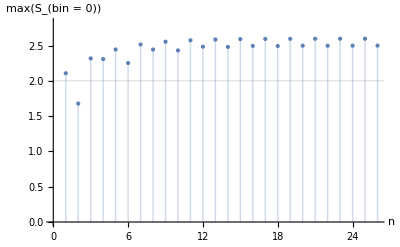

```mathematica
ClearAll[n]
a={};
Do[a=Join[a,{FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,0,π,x,y],{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[1]],FindMaximum[S1[2n,√(2n),√(2n),π/4,0,π,x,y],{x,1},{y,-2}][[1]]}],{n,1,13,1}]
ListPlot[a,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin = 0))"},PlotStyle->PointSize[Medium]]
```

## Finite bin width

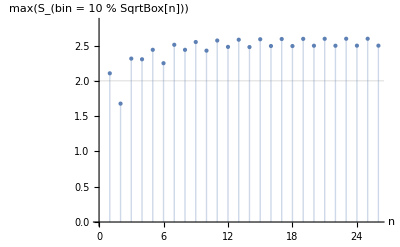

```mathematica
ClearAll[n]
a={};
Do[a=Join[a,{S2[2n-1,π/4,0,π,x,y]/.FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,0,π,x,y],{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[2]],S2[2n,π/4,0,π,x,y]/.FindMaximum[S1[2n,√(2n),√(2n),π/4,0,π,x,y],{x,1},{y,-2}][[2]]}],{n,1,13,1}]
ListPlot[a,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin = 10  % SqrtBox[n]))"},PlotStyle->PointSize[Medium]]
```

### Numerical

```mathematica
ClearAll[n,θ,a,b]
n=4;
θ=π/4;
a=0;
b=π;
aprime=0.9;
bprime=-2.2;
e1=Expec2[n,a,b,θ];
range=9;
SetSharedVariable[monitor]
Monitor[
matrix1=ParallelTable[monitor={ka,kb};Abs[e1+Expec2[n,a,(kb-(range +1))π/range,θ]+Expec2[n,(ka-(range +1))π/range,b,θ]-Expec2[n,(ka-(range +1))π/range,(kb-(range +1))π/range,θ]]
,{ka,1,2 range +1},{kb,1,2 range +1}]
,monitor];
```

```mathematica
ListContourPlot[matrix2ᵀ,DataRange->{{-π,π},{-π,π}}, AxesLabel->{"σ'_A","σ'_B"},LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]},PlotLegends->Automatic]
```

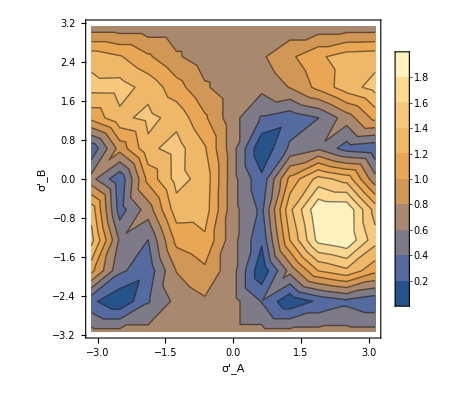

```mathematica
plot1=ListContourPlot[matrix1ᵀ,DataRange->{{-π,π},{-π,π}}, AxesLabel->{"σ'_A","σ'_B"},LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]},PlotLegends->Automatic]
```

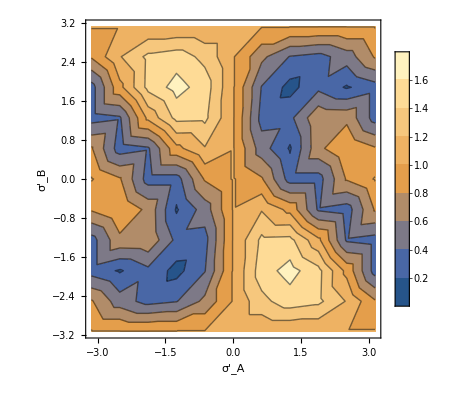

```mathematica
plot2=ListContourPlot[matrix2ᵀ,DataRange->{{-π,π},{-π,π}}, AxesLabel->{"σ'_A","σ'_B"},LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]},PlotLegends->Automatic]
```

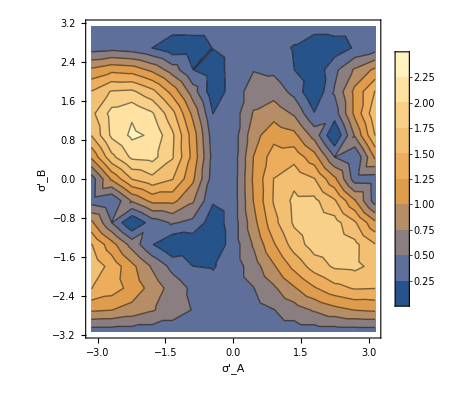

```mathematica
plot3=ListContourPlot[matrix03ᵀ,DataRange->{{-π,π},{-π,π}}, AxesLabel->{"σ'_A","σ'_B"},LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]},PlotLegends->Automatic]
```

QKD

```mathematica
(*ContourPlot[(1-Abs[Abs[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2-Abs[pmm[4,2,2,π/4,σ1,σ2]]^2]-Abs[Abs[pmp[4,2,2,π/4,σ1,σ2]]^2-Abs[ppm[4,2,2,π/4,σ1,σ2]]^2]])Abs[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2-Abs[pmp[4,2,2,π/4,σ1,σ2]]^2],{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2-Abs[pmp[4,2,2,π/4,σ1,σ2]]^2],{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[Abs[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2-Abs[pmm[4,2,2,π/4,σ1,σ2]]^2]-Abs[Abs[pmp[4,2,2,π/4,σ1,σ2]]^2-Abs[ppm[4,2,2,π/4,σ1,σ2]]^2]],{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2-Abs[pmm[4,2,2,π/4,σ1,σ2]]^2],{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[Abs[pmp[4,2,2,π/4,σ1,σ2]]^2-Abs[ppm[4,2,2,π/4,σ1,σ2]]^2],{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[ppp[4,2,2,π/4,σ1,σ2]]^2,{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[ppm[4,2,2,π/4,σ1,σ2]]^2,{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[pmp[4,2,2,π/4,σ1,σ2]]^2,{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Abs[pmm[4,2,2,π/4,σ1,σ2]]^2,{σ1,-π,π},{σ2,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_1","σ_2"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]*)
```

N=2

```mathematica
(*P1=NIntegrate[Abs[cpp[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
1.2108036454769306*^-7

3.743891846919837*^-10
P2=NIntegrate[Abs[cpm[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0002402443957300807

4.79414478575965*^-6
P3=NIntegrate[Abs[cmp[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0009457493530302007

0.00001888418221593727
P4=NIntegrate[Abs[cmm[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0007056260376649671

0.00001409041181936231
Q1=NIntegrate[Abs[cpp[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0006859469230495151


0.000013697464397229831
Q2=NIntegrate[Abs[cpm[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0009454252850185917

0.00001887763479537359
Q3=NIntegrate[Abs[cmp[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.00025992351034553294

5.18709220789213*^-6
Q4=NIntegrate[Abs[cmm[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
4.451483764561263*^-7

6.921809748374356*^-9
R1=NIntegrate[Abs[cpp[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.00012177484455630045

2.4248995785812186*^-6
R2=NIntegrate[Abs[cpm[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.00011859063153862732

2.3696195963631252*^-6
R3=NIntegrate[Abs[cmp[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0016383951798789845

0.00003272249345088419
R4=NIntegrate[Abs[cmm[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.000012980210816183706

2.521005844153865*^-7
H1=NIntegrate[Abs[cpp[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0016240894779036544

0.00003243661238532428
H2=NIntegrate[Abs[cpm[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
7.2827301644524896*^-6

1.384868072791395*^-7
H3=NIntegrate[Abs[cmp[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.0001360805465316306

2.7107806441411327*^-6
H4=NIntegrate[Abs[cmm[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
0.00012428811219035853

2.4832333734993713*^-6
ptot=
P1+P2+P3+P4
0.001891740866789796

0.000037769113210243924
qtot=Q1+Q2+Q3+Q4
0.001891740866790096
rtot=R1+R2+R3+R4
0.001891740866790096
htot=H1+H2+H3+H4
0.0018917408667900961
s=(P1-P2-P3+P4)/ptot+(Q1-Q2-Q3+Q4)/qtot+(R1-R2-R3+R4)/rtot-(H1-H2-H3+H4)/htot
-2.2341582287025847*)
```

N=4

```mathematica
(*P1=NIntegrate[Abs[cpp[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
1.2107010113156977*^-6

1.2507026699869094*^-42
P2=NIntegrate[Abs[cpm[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.00043400767330830373

0.000017326373827819462
P3=NIntegrate[Abs[cmp[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0022870362313983645

0.00009109420291913095
P4=NIntegrate[Abs[cmm[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
1.2107010113156977*^-6

1.2507026699869094*^-42
Q1=NIntegrate[Abs[cpp[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.00008309373101308356

3.2780635712314692*^-6
Q2=NIntegrate[Abs[cpm[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0003521246432594949

0.000014048310256587999
Q3=NIntegrate[Abs[cmp[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.001854569433904024

0.00007385963375266673
Q4=NIntegrate[Abs[cmm[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.00043367749845861514

0.000017234569166464252
R1=NIntegrate[Abs[cpp[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0004715180269256919

0.000018742581362868597
R2=NIntegrate[Abs[cpm[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.00034495993802088535

0.000013761482091737498
R3=NIntegrate[Abs[cmp[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0018167289054369477

0.00007235162155626238
R4=NIntegrate[Abs[cmm[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.00009025843625169323

3.564891736081962*^-6
H1=NIntegrate[Abs[cpp[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0007633675451176727

0.00003038046353534576
H2=NIntegrate[Abs[cpm[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.000053110419828904536

2.1235999192603454*^-6
H3=NIntegrate[Abs[cmp[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0011742956197994354

0.00004675723378855245
H4=NIntegrate[Abs[cmm[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
0.0007326917218892058

0.0000291592795037919
ptot=
P1+P2+P3+P4
0.0027234653067292995

0.00010842057674695042
qtot=
Q1+Q2+Q3+Q4
0.0027234653066352177

0.00010842057674695045
rtot=
R1+R2+R3+R4
0.002723465306635218

0.00010842057674695043
htot=
H1+H2+H3+H4
0.0027234653066352185

0.00010842057674695046
s=(P1-P2-P3+P4)/ptot+(Q1-Q2-Q3+Q4)/qtot+(R1-R2-R3+R4)/rtot-(H1-H2-H3+H4)/htot
-2.3048250119610167

-2.3084218458183337*)
```

```mathematica
(*cplt2=ContourPlot[Schsh[24,√24,√24,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
Export["cplt2.emf",cplt2,ImageResolution->800,ImageSize->Scaled[1]]
"cplt2.emf"
cplt =ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
Export["clpt.emf",cplt,ImageResolution->800,ImageSize->Scaled[1]]
"clpt.emf"
ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,0,2π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
ContourPlot[Schsh[2,2,2,π/4,0,π,aprime,bprime],{aprime,0,2π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]*)
```

## Effect of binning

```mathematica
n=1;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,2},{y,-1}]
```

{2.10808,{x→2.24069,y→-0.900902}}

```mathematica
n=2;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,1},{y,-2}]
```

{1.67865,{x→1.22735,y→-1.91424}}

```mathematica
n=3;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,-2},{y,1}]
```

{2.31855,{x→-2.16408,y→0.977511}}

```mathematica
n=4;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,1},{y,-2}]
```

{2.30994,{x→0.955645,y→-2.18595}}

```mathematica
n=5;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,2},{y,-1}]
```

{2.44506,{x→2.12937,y→-1.01222}}

```mathematica
n=24;
{val,sub}=FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,1},{y,-2}]
```

{2.49967,{x→1.04707,y→-2.09452}}

```mathematica
S2[n,π/4,0,π,x,y,0.1]/.sub
```

2.4994

```mathematica
S2[n,π/4,0,π,x,y,0.5]/.sub
```

2.42813

```mathematica
S2[n,π/4,0,π,x,y,0.95]/.sub
```

1.99422

```mathematica
S2[n,π/4,0,π,x,y,0.9]/.sub
```

2.03199

```mathematica
S2[n,π/4,0,π,x,y,0.8]/.sub
```

2.12553

```mathematica
S2[n,π/4,0,π,x,y,1]/.sub
```

1.96048

```mathematica
S2[n,π/4,0,π,x,y,0.6]/.sub
```

2.3434

```mathematica
S2[n,π/4,0,π,x,y,0.3]/.sub
```

2.49274

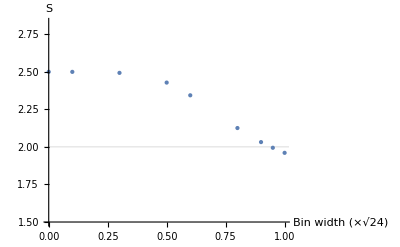

```mathematica
ListPlot[{{0,2.4996723385107824},{0.1,2.4994031742781964},{0.3,2.4927418042758496},{0.5,2.428132553296674},{0.6,2.343402504364806},{0.8,2.125528769589338},{0.9,2.0319900286056143},{0.95,1.9942218525321027},{1,1.9604832289926528}},PlotLegends-> Automatic,Filling->None,PlotRange-> {1.5,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"Bin width (×√24)","S"},PlotStyle->PointSize[Medium]]
```

```mathematica
n=7;
FindMaximum[S1[n,√n,√n,π/4,0,π,x,y],{x,-2},{y,1}]
```

{2.5165,{x→-2.11223,y→1.02936}}

## Anomalous effect of N=2

```mathematica
n=24;
{val,subs}=FindMaximum[S1[n,√n,√n,π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}]
list24={};
ClearAll[k]
Monitor[
Do[bin=k/10;list24=Join[list24,{S2[n,π/4,u,v,x,y,bin]/.subs}],{k,5,15}]
,k]
```

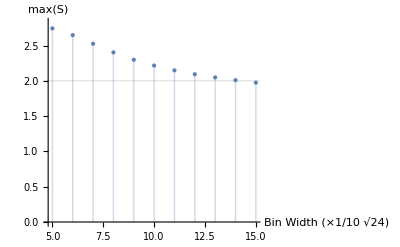

```mathematica
ListPlot[list24,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,DataRange-> {5,15},LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"Bin Width (×1/10 √24) ","max(S)"},PlotStyle->PointSize[Medium]]
```

```mathematica
bin=1;
S2[n,π/4,u,v,x,y,bin]/.subs
```

2.21705

```mathematica
bin=1.5;
S2[n,π/4,u,v,x,y,bin]/.subs
```

1.97486

```mathematica
ClearAll[n]
list={};
Do[list=Join[list,{FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[1]],FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}][[1]]}],{n,1,13,1}]
```

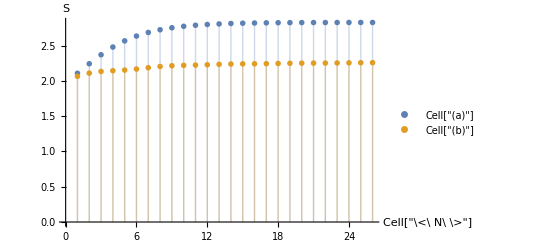

```mathematica
ListPlot[{list,list95},Filling-> Axis,PlotLegends->Placed[PointLegend[{"Cell["(a)",ExpressionUUID->"f3d6c63f-af68-485e-adc8-544a7615dd76"]","Cell["(b)",ExpressionUUID->"727797c0-c8e4-4297-b40b-90cec514071c"]"},LegendMarkerSize->{30,30}],Below],PlotRange-> {0,2 √2},GridLines->{None,{2,2 √2}}, AxesStyle->Thick,LabelStyle->{FontSize->60,FontFamily->"Times",Black},AxesLabel->{"Cell["\<\

N\
\>",ExpressionUUID->"9c0f230a-6ba2-4bd5-88d9-0237d41de271"]","S   "},PlotStyle->PointSize[0.010],ImageSize->Scaled[1]]
```

```mathematica
n=24;FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}]
```

{2.82843,{u→-0.428097,v→2.78429,x→1.1427,y→-1.9281}}

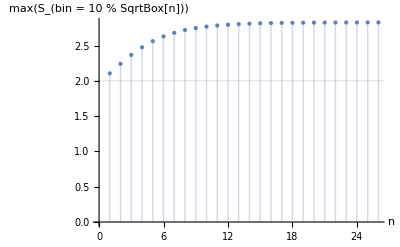

```mathematica
ClearAll[n]
list={};
bin=0.10;
Do[list=Join[list,{S2[2n-1,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[2]],S2[2n,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}][[2]]}],{n,1,13,1}]
ListPlot[list,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin=10%√n))"},PlotStyle->PointSize[Medium]]
```

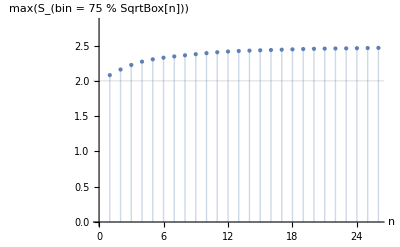

```mathematica
ClearAll[n,bin]
list75={};
bin=0.75;
Do[list75=Join[list75,{S2[2n-1,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[2]],S2[2n,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}][[2]]}],{n,1,13,1}]
ListPlot[list75,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin=75%√n))"},PlotStyle->PointSize[Medium]]
```

```mathematica
ClearAll[n,bin]
list95={};
bin=0.95;
Do[list95=Join[list95,{S2[2n-1,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[2]],S2[2n,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}][[2]]}],{n,1,13,1}]
```

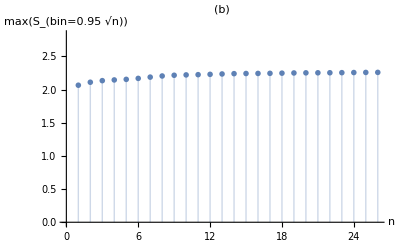

```mathematica
ListPlot[list95,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2,2 √2}}, AxesStyle->Thick,LabelStyle->{FontSize->60,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin=0.95 √n))"},PlotStyle->PointSize[0.010],PlotLabel->"(b)",ImageSize->Scaled[1]]
```

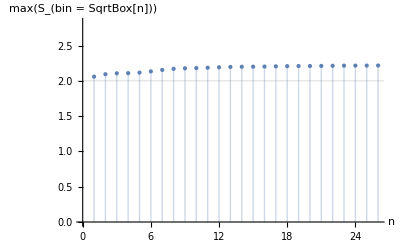

```mathematica
ClearAll[n,bin]
list100={};
bin=1;
Do[list100=Join[list100,{S2[2n-1,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n-1,√(2n-1),√(2n-1),π/4,u,v,x,y],{u,0},{v,π},{x,(-1)^(n+1)2},{y,(-1)^(n+1)(-1)}][[2]],S2[2n,π/4,u,v,x,y,bin]/.FindMaximum[S1[2n,√(2n),√(2n),π/4,u,v,x,y],{u,0},{v,π},{x,1},{y,-2}][[2]]}],{n,1,13,1}]
ListPlot[list100,PlotLegends-> Automatic,Filling-> Axis,PlotRange-> {0,2 √2},GridLines->{None,{2}}, AxesStyle->Normal,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"n","max(S_(bin = SqrtBox[n]))"},PlotStyle->PointSize[Medium]]
```

## Effects of loss

```mathematica
Subscript[f, ϕ][n_,ϕ_,R_]=(ⅇ^(R^2/2)ⅇ^(- ⅈ n ϕ)√(n!))/(2π R^n);
Ψppϕ[t_,R_,ϕ_,θ_,x_]=1/(√π)ⅇ^(ⅈ(2t R Sin[ϕ+θ])x)ⅇ^(-(x-t R Cos[ϕ+θ])^2)ⅇ^(-ⅈ(t R)^2 Cos[ϕ+θ]Sin[ϕ+θ]);
Ψpmϕ[t_,R_,ϕ_,θ_,x_]=1/(√π)ⅇ^(ⅈ t R( Sin[ϕ+θ]+ Sin[ϕ-θ])x)ⅇ^((-(x-t R Cos[ϕ+θ])^2-(x-t R Cos[ϕ-θ])^2)/2)ⅇ^(-ⅈ((t R)^2(Cos[ϕ+θ]Sin[ϕ+θ]+Cos[ϕ+θ]Sin[ϕ+θ]))/2);
Ψmpϕ[t_,R_,ϕ_,θ_,x_]=Ψpmϕ[t,R,ϕ,θ,x];
Ψmmϕ[t_,R_,ϕ_,θ_,x_]=Ψppϕ[t,R,ϕ,-θ,x];
ψ[σ1_,σ2_,Φ_,θ_,x_]=-ⅇ^(ⅈ(σ1+σ2))/4(Subscript[f, ϕ][n,Φ-θ,R]Ψppϕ[t,R,Φ-θ,θ,x]A1+Subscript[f, ϕ][n,-Φ-θ,R]Ψppϕ[t,R,-Φ-θ,θ,x]B1)-ⅇ^(ⅈ(σ1))/4(Subscript[f, ϕ][n,0,R]Ψpmϕ[t,R,0,θ,x]A2+Subscript[f, ϕ][n,π,R]Ψpmϕ[t,R,π,θ,x]B2)-ⅇ^(ⅈ(σ2))/4(Subscript[f, ϕ][n,0,R]Ψmpϕ[t,R,0,θ,x]A2+Subscript[f, ϕ][n,π,R]Ψmpϕ[t,R,π,θ,x]B2)-1/4(Subscript[f, ϕ][n,Φ+θ,R]Ψmmϕ[t,R,Φ+θ,-θ,x]A1+Subscript[f, ϕ][n,-Φ+θ,R]Ψmmϕ[t,R,-Φ+θ,-θ,x]B1);
```

```mathematica
p1=Plot3D[{Abs[Ψpmϕ[1,√24,0,π/4,x]]^2,Abs[Ψpmϕ[1,√24,π,π/4,x]]^2,Abs[Ψppϕ[1,√24,Φ-π/4,π/4,x]]^2-0.5,Abs[Ψmmϕ[1,√24,-Φ+π/4,π/4,x]]^2-1},{x,-6,6},{Φ,0,π},PlotRange-> Full,PlotLegends->{"+-;0","+-;π","++;-Φ-π/4","--;Φ-π/4"},PlotPoints->50,PlotStyle->{Opacity[0.2],Opacity[ 0.2],Opacity[0.5],Opacity[1]},Mesh-> None,AxesLabel-> {"x","Φ"}]
```

-Graphics3D-

```mathematica
p2=Plot3D[{Abs[ψ[0,π,Φ,π/4,x]]^2},{x,-6,6},{Φ,0,π},PlotRange-> Full,PlotLegends->Automatic,PlotPoints->50,PlotStyle->{Opacity[0.5],Opacity[0.5],Opacity[0.5]},Mesh->None,AxesLabel-> {"x","Φ"}]
```

-Graphics3D-

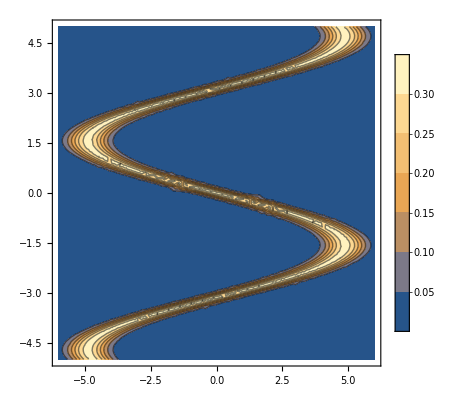

```mathematica
ContourPlot[Abs[Ψmmϕ[1,√24,-Φ-π/4,π/4,x]]^2,{x,-6,6},{Φ,-5,5},PlotRange-> Full,PlotLegends->Automatic]
```

### Backup

```mathematica
list24={2.7439725988406605,2.6487079312528854,2.5269113292945455,2.404390956699423,2.2992827561572744,2.217051938277966,2.1498004676431126,2.0942515452321877,2.0488636228702157,2.009726464805063,1.9748638564606553};
```

```mathematica
list100={2.060113865767819,2.0947318160046247,2.1072490320489345,2.110104172656901,2.1174675765911912,2.1347577082984284,2.1554072111840794,2.1705951055826804,2.178116530183154,2.1820452514168767,2.186896389914955,2.1930996786304364,2.1980914882672957,2.200400667620092,2.201361402266558,2.20317624885344,2.2062606663549094,2.2091366729033,2.210594586805649,2.2111338080833325,2.212123212717099,2.2140279581881455,2.2159805969494535,2.217051938277966,2.2174169499814487,2.2180142301906334};
```

```mathematica
list95={2.0649576010986164,2.1099052213198686,2.1337378607394797,2.144439307812151,2.1532531043355174,2.167818401997872,2.1869462989276505,2.2041404250338807,2.2150057076576823,2.220331576975966,2.2239702886160138,2.2287911324815077,2.234508726681754,2.2390751356365515,2.2414215163218896,2.2425004467326417,2.244038655105626,2.2466757699931796,2.2495217900319946,2.2514045163439778,2.2521901896425347,2.2527936648334785,2.2540723793249073,2.2559184783383346,2.257515759548042,2.2583320658933603};
```

```mathematica
list75={2.0815357952727407,2.1614659625254466,2.225770651309695,2.27294406845757,2.3057390099578488,2.328751299094196,2.346633937255569,2.362738687973848,2.378406447593512,2.3932467363904766,2.4061536873888087,2.4163179060831004,2.423721832162304,2.429087573545245,2.4334774705478166,2.437787060109734,2.4423829488051596,2.4470681483161725,2.451355335946657,2.4548384689651814,2.457437995840361,2.4594191040768,2.461216029894356,2.463181217903242,2.4654071418892234,2.4677188108278125};
```

```mathematica
matrix1=Abs[{{-0.6666666666666665,0.24436900680666393,1.0620640254769067,1.4740866846435061,1.3230583326399308,0.6666666666666665,-0.24436900680666582,-1.0620640254769085,-1.4740866846435061,-1.3230583326399301,-0.6666666666666665},{-0.6666666666666665,-0.03262898913656187,0.4398795220735746,0.570376675655089,0.3090169943749489,-0.244369006806664,-0.878406684336767,-1.350915195546907,-1.481412349128417,-1.2200526678482797,-0.6666666666666665},{-0.6666666666666665,-0.37781549659666647,-0.27480983180501406,-0.39699433520834926,-0.6976986794051159,-1.0620640254769032,-1.3509151955469045,-1.4539208603385574,-1.331736356935222,-1.0310320127384514,-0.6666666666666665},{-0.6666666666666665,-0.6593410021817528,-0.8090169943749492,-1.0585235015283123,-1.3125575183235352,-1.4740866846435021,-1.4814123491284166,-1.331736356935222,-1.0822298497818559,-0.8281958329866307,-0.6666666666666665},{-0.6666666666666665,-0.7696723314583153,-0.9586929865681431,-1.1615291663199638,-1.3007043441967685,-1.32305833263993,-1.2200526678482788,-1.0310320127384527,-0.8281958329866324,-0.6890206551098278,-0.6666666666666665},{-0.6666666666666665,-0.6666666666666665,-0.6666666666666665,-0.6666666666666666,-0.6666666666666665,-0.6666666666666665,-0.6666666666666665,-0.6666666666666665,-0.6666666666666665,-0.6666666666666665,-0.6666666666666665},{-0.6666666666666665,-0.3896686707234398,-0.044482163263334845,0.23704334232174998,0.34737467159831437,0.24436900680666204,-0.03262898913656409,-0.3778154965966707,-0.6593410021817535,-0.7696723314583165,-0.6666666666666665},{-0.6666666666666665,-0.04448216326333826,0.6702071906152547,1.2044143531851856,1.3540903453783812,1.0620640254769023,0.43987952207357095,-0.27480983180502216,-0.8090169943749488,-0.9586929865681444,-0.6666666666666665},{-0.6666666666666665,0.2370433423217531,1.2044143531851887,1.865943519505152,1.9689491842968012,1.4740866846435021,0.5703766756550834,-0.3969943352083529,-1.0585235015283154,-1.1615291663199643,-0.6666666666666665},{-0.6666666666666665,0.34737467159831625,1.3540903453783846,1.9689491842968025,1.9570960101700325,1.3230583326399294,0.30901699437494834,-0.6976986794051221,-1.3125575183235405,-1.3007043441967698,-0.6666666666666665},{-0.6666666666666665,0.24436900680666543,1.0620640254769071,1.4740866846435057,1.3230583326399308,0.6666666666666665,-0.24436900680666582,-1.0620640254769085,-1.4740866846435057,-1.3230583326399301,-0.6666666666666665}}];
```

```mathematica
matrix2={{1.015384262773814,0.8214631244048933,0.3137709930179835,0.3137709930179851,0.8214631244048929,1.015384262773814,0.8214631244048936,0.31377099301798395,0.31377099301798494,0.8214631244048931,1.015384262773814},{1.015384262773814,0.49448944252233085,0.17824789583476786,0.7458649545462068,0.9915513097784623,0.8214631244048936,0.3005683041534099,0.3721690342036894,0.9397860929151272,1.1854724481473826,1.015384262773814},{1.015384262773814,0.329444235552141,0.3483360812083368,0.7590676434107819,0.7458649545462068,0.3137709930179851,0.3721690342036885,1.049949350964166,1.4606809131666108,1.4474782243020354,1.015384262773814},{1.015384262773814,0.38936916287667134,0.13152565737481337,0.3483360812083381,0.17824789583476813,0.3137709930179835,0.9397860929151255,1.4606809131666105,1.6774913370001343,1.507403151626565,1.015384262773814},{1.015384262773814,0.6513749390313247,0.3893691628766721,0.3294442355521413,0.49448944252233,0.8214631244048937,1.1854724481473826,1.4474782243020365,1.5074031516265665,1.3423579446563771,1.015384262773814},{1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814,1.015384262773814},{1.015384262773814,1.3423579446563771,1.5074031516265662,1.4474782243020357,1.185472448147383,0.821463124404893,0.49448944252232935,0.32944423555214186,0.3893691628766714,0.6513749390313242,1.015384262773814},{1.015384262773814,1.5074031516265674,1.6774913370001356,1.4606809131666108,0.9397860929151283,0.3137709930179854,0.17824789583476697,0.3483360812083357,0.13152565737481137,0.38936916287667134,1.015384262773814},{1.015384262773814,1.4474782243020357,1.4606809131666114,1.0499493509641658,0.37216903420368935,0.3137709930179836,0.745864954546206,0.7590676434107813,0.34833608120833626,0.329444235552141,1.015384262773814},{1.015384262773814,1.1854724481473828,0.9397860929151272,0.3721690342036882,0.30056830415340935,0.8214631244048933,0.9915513097784623,0.7458649545462059,0.17824789583476752,0.49448944252232924,1.015384262773814},{1.015384262773814,0.8214631244048933,0.3137709930179835,0.3137709930179851,0.8214631244048929,1.015384262773814,0.8214631244048936,0.31377099301798395,0.31377099301798494,0.8214631244048931,1.015384262773814}};
```

```mathematica
matrix3={{0.363636856231323,1.2560185197743956,1.6686437992629792,1.443903862549861,0.6676417268299534,0.3636368562313247,1.2560185197743974,1.668643799262982,1.4439038625498628,0.667641726829955,0.363636856231323},{0.363636856231323,1.1417737716845346,1.3133621815492742,0.812861145332762,0.16855495253483954,1.2560185197743965,2.0341554352276088,2.2057438450923486,1.705242808875834,0.7238267110082344,0.363636856231323},{0.363636856231323,0.9007369020606905,0.8445519178824115,0.2165426579952121,0.7434126855736579,1.6686437992629812,2.205743845092349,2.1495588609140692,1.5215496010268696,0.5615942574579987,0.363636856231323},{0.363636856231323,0.6249758025572958,0.44128259470833264,0.11727820541976264,0.837355356961392,1.443903862549863,1.705242808875835,1.52154960102687,0.9629888008987753,0.24291164935714682,0.363636856231323},{0.363636856231323,0.4198218404096035,0.2575893868593677,0.06109322124148264,0.41450005922188426,0.6676417268299527,0.7238267110082335,0.5615942574579965,0.24291164935714604,0.11049518862325636,0.363636856231323},{0.363636856231323,0.363636856231323,0.3636368562313229,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323},{0.363636856231323,0.47788160432118376,0.7189184739450272,0.9946795734484237,1.1998335355961156,1.2560185197743952,1.1417737716845338,0.9007369020606901,0.6249758025572959,0.41982184040960213,0.363636856231323},{0.363636856231323,0.7189184739450282,1.187728737611891,1.5909980607859717,1.7746912686349359,1.66864379926298,1.3133621815492744,0.8445519178824112,0.44128259470833064,0.25758938685936833,0.363636856231323},{0.363636856231323,0.9946795734484241,1.5909980607859713,1.9248189242009488,1.8686339400226695,1.4439038625498617,0.8128611453327618,0.21654265799521422,0.11727820541976236,0.06109322124148375,0.363636856231323},{0.363636856231323,1.1998335355961158,1.7746912686349363,1.8686339400226688,1.4457786422831624,0.6676417268299527,0.16855495253484043,0.743412685573658,0.837355356961392,0.4145000592218856,0.363636856231323},{0.363636856231323,1.2560185197743956,1.6686437992629792,1.443903862549861,0.6676417268299534,0.3636368562313247,1.2560185197743974,1.668643799262982,1.4439038625498628,0.667641726829955,0.363636856231323}};
```

```mathematica
matrix03={{0.363636856231323,1.0376168460588455,1.5060840939889084,1.6762529161952109,1.514419290456146,1.0526363511085046,0.3823658726861802,0.3636368562313247,1.0376168460588473,1.5060840939889106,1.6762529161952129,1.5144192904561478,1.0526363511085064,0.3823658726861822,0.363636856231323},{0.363636856231323,1.003316967505678,1.3775328470866985,1.4121664505667848,1.100358168023432,0.5038654538919822,0.25916899429077167,1.0376168460588473,1.6772969573332022,2.0515128369142226,2.086146440394308,1.774338157850956,1.177845443719506,0.41481099553675194,0.363636856231323},{0.363636856231323,0.9090655991566344,1.1613049078941629,1.070395693836332,0.6543436417556363,0.004447036889774214,0.775494768656727,1.506084093988911,2.051512836914223,2.303752145651751,2.2128429315939204,1.7967908795132264,1.138000200867812,0.3669524691008615,0.363636856231323},{0.363636856231323,0.7735303804304187,0.9002268716300303,0.7186325359175818,0.2647143585892967,0.37162359839384795,1.0643467984784416,1.6762529161952124,2.086146440394309,2.2128429315939195,2.03124859588147,1.5773304185531836,0.9409924615700398,0.24826926148544626,0.363636856231323},{0.363636856231323,0.6235557236261324,0.6460084452884018,0.4265479843283596,0.008641176545066576,0.5249404094893472,1.0685143967120592,1.5144192904561475,1.774338157850957,1.7967908795132255,1.577330418553185,1.159423610769891,0.6258420247354765,0.08226803751276335,0.363636856231323},{0.363636856231323,0.4888459488423215,0.4490007059906275,0.25199296669285665,0.06315747014170692,0.434031195431516,0.7871721194151745,1.0526363511085082,1.177845443719506,1.138000200867812,0.9409924615700413,0.6258420247354775,0.254968299445668,0.09817262453799158,0.363636856231323},{0.363636856231323,0.3960819790818911,0.3482234526460015,0.2295402450305878,0.0635390210579061,0.11690164099285005,0.27604325504302984,0.3823658726861834,0.4148109955367518,0.36695246910086,0.24826926148544826,0.08226803751276512,0.09817262453799136,0.2573142385881727,0.363636856231323},{0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323,0.36363685623132314,0.363636856231323,0.363636856231323,0.363636856231323,0.363636856231323},{0.363636856231323,0.39793673478449065,0.4921881031335339,0.6277233218597503,0.7776979786640376,0.9124077534478465,1.005171723208276,1.037616846058846,1.0033169675056781,0.9090655991566355,0.7735303804304196,0.6235557236261319,0.48884594884232335,0.39608197908189374,0.363636856231323},{0.363636856231323,0.49218810313353345,0.7084160423260686,0.9694940785902016,1.2237125049318305,1.4207202442296025,1.52149749757423,1.5060840939889097,1.3775328470866985,1.1613049078941637,0.9002268716300307,0.6460084452883997,0.44900070599063047,0.348223452646002,0.363636856231323},{0.363636856231323,0.6277233218597493,0.9694940785902016,1.321257236508952,1.6133417880981742,1.787896805733678,1.8103495273959465,1.6762529161952113,1.4121664505667841,1.0703956938363328,0.7186325359175826,0.4265479843283616,0.2519929666928581,0.229540245030589,0.363636856231323},{0.363636856231323,0.7776979786640359,1.2237125049318296,1.6133417880981744,1.869414970142404,1.941213616829176,1.8145171256295645,1.5144192904561462,1.100358168023433,0.6543436417556386,0.26471435858929493,0.008641176545066465,0.06315747014170597,0.06353902105790643,0.363636856231323},{0.363636856231323,0.9124077534478467,1.4207202442296045,1.7878968057336762,1.941213616829177,1.8503044027713451,1.5331748483326804,1.0526363511085068,0.5038654538919827,0.004447036889774325,0.37162359839384684,0.5249404094893463,0.434031195431514,0.11690164099284794,0.363636856231323},{0.363636856231323,1.0051717232082764,1.5214974975742306,1.810349527395945,1.814517125629564,1.5331748483326786,1.022045983960536,0.3823658726861806,0.2591689942907731,0.7754947686567268,1.0643467984784414,1.0685143967120596,0.787172119415173,0.2760432550430286,0.363636856231323},{0.363636856231323,1.0376168460588455,1.5060840939889084,1.6762529161952109,1.514419290456146,1.0526363511085046,0.3823658726861802,0.3636368562313247,1.0376168460588473,1.5060840939889106,1.6762529161952129,1.5144192904561478,1.0526363511085064,0.3823658726861822,0.363636856231323}};
```